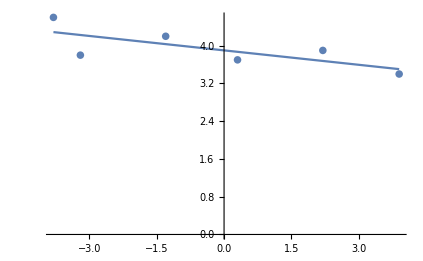

```mathematica
ax = -3.8 
ay = 4.6
bx = -3.2
by =3.8
cx = -1.3
cy = 4.2
dx = 0.3
dy = 3.7
ex = 2.2
ey = 3.9
fx = 3.9
fy = 3.4

XYAv = (ax*ay + bx*by + cx*cy + dx*dy + ex*ey + fx*fy) / 6
XAv = (ax + bx + cx + dx + ex + fx) / 6
YAv = (ay + by + cy + dy + ey + fy) / 6
XPowAv =(ax^2 + bx^2 + cx^2 + dx^2 + ex^2 + fx^2) / 6
XAvPow =XAv^2

coefA = (XYAv - XAv*YAv) / (XPowAv - XAvPow)
coefB = YAv - coefA*XAv

resultAX = ax
resultAY = ax * coefA + coefB
resultNX = fx
resultNY = fx * coefA +coefB

Show[ListPlot[{{ax,ay}, {bx,by}, {cx,cy}, {dx,dy}, {ex,ey}, {fx,fy}},  AxesOrigin-> {0,0}], ListLinePlot[{{resultAX, resultAY}, {resultNX, resultNY}},  AxesOrigin-> {0,0}]]
```